# ComplexBubblePlot

Visualize a complex function as an array of bubbles

## Definition

```mathematica
SetAttributes[ComplexBubblePlot,HoldAll];
```

```mathematica
Options[ComplexBubblePlot]={AlignmentPoint->Center,AspectRatio->Automatic,Axes->None,AxesLabel->None,AxesOrigin->Automatic,AxesStyle->{},Background->None,BaselinePosition->Automatic,BaseStyle->{},ColorFunction->Automatic,ColorFunctionScaling->True,ColorOutput->Automatic,ContentSelectable->Automatic,CoordinatesToolOptions->Automatic,DisplayFunction:>$DisplayFunction,Epilog->{},FormatType:>TraditionalForm,Frame->Automatic,FrameLabel->None,FrameStyle->{},FrameTicks->Automatic,FrameTicksStyle->{},GridLines->None,GridLinesStyle->{},ImageMargins->0.,ImagePadding->All,ImageSize->Automatic,ImageSizeRaw->Automatic,LabelStyle->{},Method->Automatic,PlotLabel->None,PlotLegends->None,PlotPoints->Automatic,PlotRange->Automatic,PlotRangeClipping->True,PlotRangePadding->Automatic,PlotRegion->Automatic,PreserveImageOptions->Automatic,Prolog->{},RotateLabel->True,Ticks->Automatic,TicksStyle->{},WorkingPrecision->MachinePrecision};
```

```mathematica
ComplexBubblePlot[f_,{z_,zmin_,zmax_},opts:OptionsPattern[]]:=Module[{cf,ff,gr,gopts,lr,pp,tf,wa,wp,xmin,xmax,ymin,ymax},
ff=Function[z,f,{Listable}];
{xmin,ymin}=ReIm[zmin];{xmax,ymax}=ReIm[zmax];
pp=Replace[OptionValue[PlotPoints]/.Automatic->25,m_Integer:>{m,m}];
wp=OptionValue[WorkingPrecision];
wa=Quiet[ff[SetPrecision[Outer[Plus,I Subdivide[ymax,ymin,Last[pp]-1],Subdivide[xmin,xmax,First[pp]-1]],wp]]];
cf=OptionValue[ColorFunction];
If[cf===Automatic,
cf=ColorData["MidShiftBalancedHue"];
tf=#/(2Pi)+1/2&,
If[StringQ[cf],cf=ColorData[cf]];
If[TrueQ[OptionValue[ColorFunctionScaling]],
tf=(#/(2Pi)+1/2)&,
tf=Identity]];
gopts=FilterRules[Join[{opts},Options[ComplexBubblePlot]],Options[Graphics]]/.
{(PlotRange->Automatic)->(PlotRange->{{xmin,xmax},{ymin,ymax}}),(PlotRangePadding->Automatic)->(PlotRangePadding->Scaled[1/6])};
gr=Graphics[{EdgeForm[Directive[Opacity[2/3,Black],AbsoluteThickness[0.6]]],Map[If[NumericQ[#],{Composition[cf,tf][Arg[#]],Disk[ReIm[#],Abs[#]/Max[pp]]},Nothing]&,wa,{2}]},Sequence@@gopts];
If[TrueQ[OptionValue[PlotLegends]===Automatic],
lr=If[TrueQ[OptionValue[ColorFunctionScaling]],{0,1},{-Pi,Pi}];
gr=Legended[gr,BarLegend[{cf,lr+If[TrueQ[OptionValue[ColorFunctionScaling]],{0,0},{-0.01,0.01}]},ColorFunctionScaling->OptionValue[ColorFunctionScaling],LegendLayout->"Column",Ticks->Rescale[FindDivisions[{0,1},{4,5}],{0,1},lr],Charting`TickLabels->{"-π","-π/2","0","π/2","π"},Charting`TickSide->Right]]];
gr]
```

```mathematica
ComplexBubblePlot[f_,{z_,w_?Internal`RealValuedNumericQ},opts:OptionsPattern[]]:=ComplexBubblePlot[f,{z,-w-w I,w+w I},opts]
```

## Documentation

### Usage

ComplexBubblePlot[f,{z,z_min,z_max}]

generates a plot of f as an array of disks scaled by Abs[f], over the complex rectangle with corners z_min and z_max.

### Details & Options

In a complex bubble plot, each disk has its center at {Re[f[z]],Im[f[z]]}, with the radius a scaling of Abs[f[z]], and colored by Arg[f[z]].

ComplexBubblePlot[f,{z,n}] is equivalent to ComplexBubblePlot[f,{z,-n-n I,n+n I}].

ComplexBubblePlot treats the variable z as local, effectively using Block.

ComplexBubblePlot has attribute HoldAll and evaluates f only after assigning specific numerical values to z. In some cases, it may be more efficient to use Evaluate to evaluate f symbolically first.

ComplexBubblePlot has the same options as Graphics, with the following additions and changes:

ColorFunction | Automatic | how to apply coloring to disks
ColorFunctionScaling | True | whether to scale arguments to ColorFunction
Frame | Automatic | whether to put a frame around the plot
PlotLegends | None | legends for color gradients
PlotPoints | Automatic | the number of disks in each direction
PlotRange | Automatic | range of values to include
PlotRangeClipping | True | whether to clip at the plot range
WorkingPrecision | MachinePrecision | the precision used in internal computations

ColorFunction is supplied with a single argument, given by default by the scaled value of Arg[f[z]].

## Examples

### Basic Examples

Plot a complex function:

```mathematica
ComplexBubblePlot[(z^2+1)/(z^2-1),{z,-2-2ⅈ,2+2ⅈ}]
```

-Graphics-

Include a legend showing how the colors vary from -π to π:

```mathematica
ComplexBubblePlot[(z^2+1)/(z^2-1),{z,-2-2ⅈ,2+2ⅈ},PlotLegends->Automatic]
```

-Graphics-

### Scope

The identity function:

```mathematica
ComplexBubblePlot[z,{z,-1-ⅈ,1+ⅈ}]
```

-Graphics-

Visualize various Power functions:

```mathematica
Table[ComplexBubblePlot[z^a,{z,-1-ⅈ,1+ⅈ},PlotLabel->ToString[z^a,TraditionalForm]],{a,{-1,1/2,2,3}}]//Partition[#,2]&//GraphicsGrid
```

-Graphics-

Visualize a function with an essential singularity:

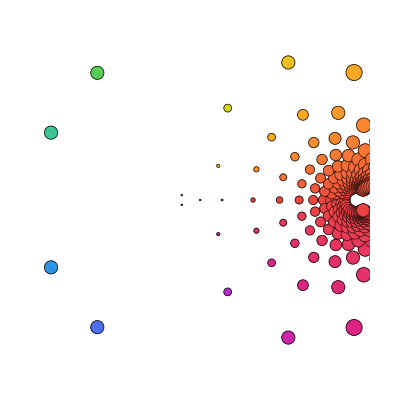

```mathematica
ComplexBubblePlot[Exp[-1/(8z^2)],{z,-1-ⅈ,1+ⅈ}]
```

### Options

#### ColorFunction

Use a different color function:

```mathematica
ComplexBubblePlot[Sin[z],{z,-1-ⅈ,1+ⅈ},ColorFunction->(ColorData["M10DefaultDensityGradient",1-Abs[2Mod[#,1]-1]]&)]
```

-Graphics-

#### ColorFunctionScaling

Arg[f] is scaled by default. Use ColorFunctionScaling to change it:

```mathematica
ComplexBubblePlot[Sin[z],{z,-1-ⅈ,1+ⅈ},ColorFunction->Hue,ColorFunctionScaling->False,PlotLegends->Automatic]
```

-Graphics-

#### PlotLegends

The Automatic legend shows the association between color and phase:

```mathematica
ComplexBubblePlot[Sin[z],{z,-1-ⅈ,1+ⅈ},PlotLegends->Automatic]
```

-Graphics-

#### PlotPoints

Use more disks:

```mathematica
ComplexBubblePlot[Sin[z],{z,-1-ⅈ,1+ⅈ},PlotPoints->35]
```

-Graphics-

#### WorkingPrecision

Evaluate functions using arbitrary-precision arithmetic:

```mathematica
ComplexBubblePlot[JacobiSD[z EllipticK[1/2],1/2],{z,-1-ⅈ,1+ⅈ},WorkingPrecision->25]
```

-Graphics-

### Neat Examples

Visualize the function -i z^a with varying a:

```mathematica
Manipulate[ComplexBubblePlot[-ⅈ z^a,{z,1},ColorFunction->(ColorData["M10DefaultDensityGradient",1-Abs[2Mod[#,1]-1]]&)],{{a,1},0.1,4,0.1},SaveDefinitions->True]
```

-Graphics-

## Source & Additional Information

### Contributed By

Jan Mangaldan

### Keywords

champagne portrait

complex bubble plot

complex functions

plotting

visualization

### Categories

Higher Mathematical Computation

Visualization & Graphics

### Related Symbols

BubbleChart

ComplexPlot

ComplexPlot3D

DensityPlot

StreamPlot

StreamDensityPlot

### Related Resource Objects

ComplexD

ComplexToPolar

RiemannSurfacePlot3D

RiemannSphereComplexPlot

### Source/Reference Citation

Source, reference or citation information

### Links

Cleve's Corner–Champagne Portraits of Complex Functions

### Tests

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.